vl^3/(4 (0.4+vl)^2)+0.025 (-1.55556+(2 vl)/(0.4+vl))^2

((0.5 vl+2 vl^2-0.02 (0.4+vl))^2)/(16 vl (0.4+vl)^2)+(0.0120563 (0.08 (0.4+vl)+0.4 (0.16+2 (1.+vl)-0.4 (6.5+vl)))^2)/(0.4+vl)^2

vl^3/(4 (0.6+vl)^2)+0.0375 (-1.58824+(2 vl)/(0.6+vl))^2

((0.5 vl+2 vl^2-0.02 (0.6+vl))^2)/(16 vl (0.6+vl)^2)+(0.00901096 (0.08 (0.6+vl)+0.6 (0.36+2 (1.+vl)-0.6 (6.5+vl)))^2)/(0.6+vl)^2

vl^3/(4 (0.8+vl)^2)+0.05 (-1.625+(2 vl)/(0.8+vl))^2

((0.5 vl+2 vl^2-0.02 (0.8+vl))^2)/(16 vl (0.8+vl)^2)+(0.00762939 (0.08 (0.8+vl)+0.8 (0.64+2 (1.+vl)-0.8 (6.5+vl)))^2)/(0.8+vl)^2

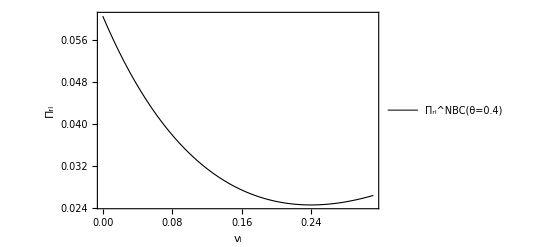

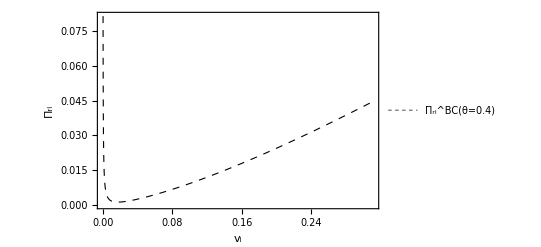

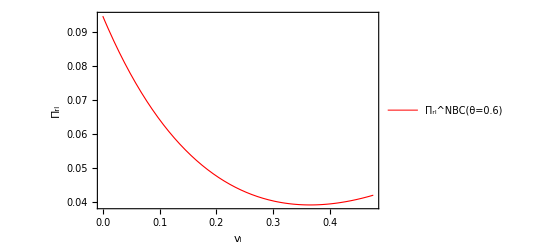

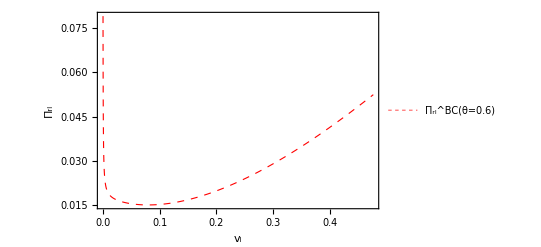

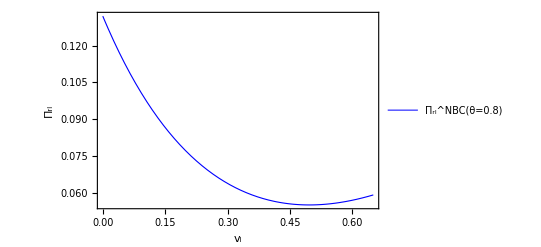

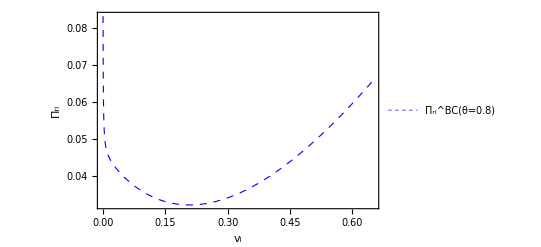

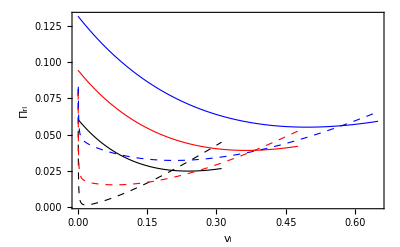

```mathematica
rlNBC1=vl^3/(4 (vl+θ)^2)+1/16 θ (-1+2/(-4+θ)+(2 vl)/(vl+θ))^2/.{θ->0.4}
rlBC1=((2 cg vl+2 vl^2-cm (vl+θ))^2)/(16 vl (vl+θ)^2)+((4 cm (vl+θ)+θ (2 (4 cg+vl)-(6+2 cg+vl) θ+θ^2))^2)/(16 (-4+θ)^2 θ (vl+θ)^2)/.{θ->0.4,cg->0.25,cm ->0.02}
rlNBC2=vl^3/(4 (vl+θ)^2)+1/16 θ (-1+2/(-4+θ)+(2 vl)/(vl+θ))^2/.{θ->0.6}
rlBC2=((2 cg vl+2 vl^2-cm (vl+θ))^2)/(16 vl (vl+θ)^2)+((4 cm (vl+θ)+θ (2 (4 cg+vl)-(6+2 cg+vl) θ+θ^2))^2)/(16 (-4+θ)^2 θ (vl+θ)^2)/.{θ->0.6,cg->0.25,cm ->0.02}
rlNBC3=vl^3/(4 (vl+θ)^2)+1/16 θ (-1+2/(-4+θ)+(2 vl)/(vl+θ))^2/.{θ->0.8}
rlBC3=((2 cg vl+2 vl^2-cm (vl+θ))^2)/(16 vl (vl+θ)^2)+((4 cm (vl+θ)+θ (2 (4 cg+vl)-(6+2 cg+vl) θ+θ^2))^2)/(16 (-4+θ)^2 θ (vl+θ)^2)/.{θ->0.8,cg->0.25,cm ->0.02}
arl1=Plot[{rlNBC1},{vl,0,0.31111},PlotRange->Automatic,Frame->True,FrameLabel->{"v_l","Π_rl"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"Π_rl^NBC(θ=0.4)"},Center]]
brl2=Plot[{rlBC1},{vl,0,0.31111},PlotRange->Automatic,Frame->True,FrameLabel->{"v_l","Π_rl"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"Π_rl^BC(θ=0.4)"},Center]]
crl1=Plot[{rlNBC2},{vl,0,0.4765},PlotRange->Automatic,Frame->True,FrameLabel->{"v_l","Π_rl"},PlotStyle->{Thickness[0.002],Red},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"Π_rl^NBC(θ=0.6)"},Center]]
drl2=Plot[{rlBC2},{vl,0,0.4765},PlotRange->Automatic,Frame->True,FrameLabel->{"v_l","Π_rl"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"Π_rl^BC(θ=0.6)"},Center]]
erl1=Plot[{rlNBC3},{vl,0,0.65},PlotRange->Automatic,Frame->True,FrameLabel->{"v_l","Π_rl"},PlotStyle->{Thickness[0.002],Blue},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"Π_rl^NBC(θ=0.8)"},Center]]
frl2=Plot[{rlBC3},{vl,0,0.65},PlotRange->Automatic,Frame->True,FrameLabel->{"v_l","Π_rl"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"Π_rl^BC(θ=0.8)"},Center]]
Show[arl1,brl2,crl1,drl2,erl1,frl2,PlotRange->All,Axes->False]
```